```mathematica
Off[General::munfl]
```

```mathematica
lecnbr=5;
lecs={{1.00,0.0036,-30.9795},{2.00,0.0036,-117.5248},{3.00,0.0036,-259.7207},{4.00,0.0036,-457.5555},{5.00,0.0036,-711.0607},{6.00,0.0036,-1020.1831},{7.00,0.0036,-1385.0069},{8.00,0.0036,-1805.4404},{9.00,0.0036,-2281.5596}};
```

## Finite differences

```mathematica
SolveSecular[Ene_?NumberQ, Rdis_?NumberQ,Npoints_?NumberQ,Local_:False]:=Block[{e,Rmax,nGrid,hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,asywf,fit,mod,usol},
e=Ene;
Rmax=Rdis;
nGrid=Npoints;
hDif=Rmax/nGrid;
L=0;

(* Matrix components *)
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{nGrid,nGrid}];
Dmat=DiagonalMatrix[Table[hDif^2 mh2(e-V0[i hDif])+(L(L+1))/i^2,{i,1,nGrid}]];
If[Local≠True,
Wmat=Table[hDif^2 mh2 W[i hDif,j hDif, e],{i,1,nGrid},{j,1,nGrid}]; 
,
(*Print[">> ... Local approximation ..."];*)
Wmat=DiagonalMatrix[Table[hDif^2 mh2 W[i hDif,i hDif, e],{i,1,nGrid}]]; ];

If[e==0, 
bcol=Table[Which[i==nGrid,-hDif,1==1,0],{i,1,nGrid}];
Dmat⟦nGrid⟧⟦nGrid⟧+=1; (*this is only for 0 energy*)
,
bcol=Table[Which[i==nGrid,-1,1==1,0],{i,1,nGrid}];
];
ucol=Array[Subscript["u", ##]&,{nGrid}];
Amat=Dmat+Wmat+Kmat;


usol=LinearSolve[Amat,bcol];
wf=Table[{i hDif,usol⟦i⟧},{i,1,nGrid}];

If[e==0, 
wffree=Table[{i hDif,(usol[[-1]]-usol[[-2]]) i+usol[[-2]]-(usol[[-1]]-usol[[-2]]) nGrid},{i,1,nGrid}];
Tere=Rmax-usol⟦-1⟧;
,
asywf=nn Sin[Sqrt[2 μ/hbar^2 e] r+δ];
fit=FindFit[wf,asywf,{nn,δ},r];
mod=Function[{r},Evaluate[asywf/.fit]];wffree=Table[{i hDif,mod[i hDif]},{i,1,nGrid}];
Tere=-(hbar/Sqrt[2 μ e]) Tan[δ/.fit[[2]]];
];
Tere
]
```

### nucleon-nucleon EFT_nopi leading-order benchmark

μ = 469.46     hbarc = 197.327     h^2/2μ = 41.471      E_0 = 0.01MeV

20.2133

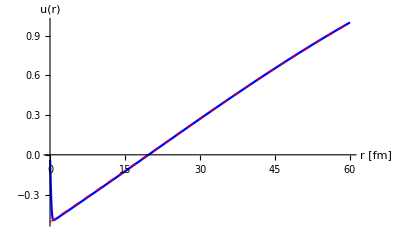

20.3192

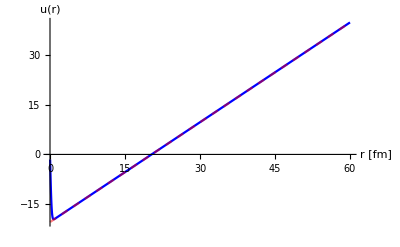

```mathematica
Rmax=60;nGrid=2500;
μ=938.92/2;hbar=197.327053;mh2=(μ 2)/(hbar)^2;e0=0.01;
Print["μ = ", μ, "     hbarc = ",hbar, "     h^2/2μ = ", N[1/mh2 ],"      E_0 = ",e0,"MeV"];

Λ=lecs[[lecnbr]][[1]];λ=0.25 Λ^2;
C0=lecs[[lecnbr]][[3]];
V0[r_]:= C0 Exp[- Λ^2 r^2/4];
W[r_,rp_,e_]:=0;


a0=SolveSecular[e0,Rmax,nGrid,True]
ListLinePlot[{wf,wffree},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},AxesLabel->{"r [fm]","u(r)"},PlotRange->{Automatic,Automatic}]

a0=SolveSecular[0.0,Rmax,nGrid,True]
ListLinePlot[{wf,wffree},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},AxesLabel->{"r [fm]","u(r)"},PlotRange->{Automatic,Automatic}]
```

Λ = 1. fm^-2     C_0 = -30.9795 MeV     a_0 = 21.8387 fm

Λ = 2. fm^-2     C_0 = -117.525 MeV     a_0 = 21.0723 fm

Λ = 3. fm^-2     C_0 = -259.721 MeV     a_0 = 20.7748 fm

Λ = 4. fm^-2     C_0 = -457.556 MeV     a_0 = 20.5714 fm

Λ = 5. fm^-2     C_0 = -711.061 MeV     a_0 = 20.3192 fm

Λ = 6. fm^-2     C_0 = -1020.18 MeV     a_0 = 20.0526 fm

Λ = 7. fm^-2     C_0 = -1385.01 MeV     a_0 = 19.6587 fm

Λ = 8. fm^-2     C_0 = -1805.44 MeV     a_0 = 19.2162 fm

Λ = 9. fm^-2     C_0 = -2281.56 MeV     a_0 = 18.6582 fm

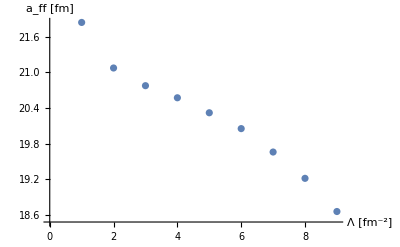

```mathematica
affofL={};
μ=938.92/2;hbar=197.327053;mh2=(μ 2)/(hbar)^2;e0=0.0;
Do[
Λ=pot[[1]];λ=0.25 Λ^2;
C0=pot[[3]];
V0[r_]:= C0 Exp[- Λ^2 r^2/4];
W[r_,rp_,e_]:=0;
a0=SolveSecular[e0,Rmax,nGrid,True];
AppendTo[affofL,{Λ,a0}];
Print["Λ = ",Λ," fm^-2     C_0 = ",C0," MeV     a_0 = ",a0," fm"]
,{pot,lecs}]
ListPlot[affofL,AxesLabel->{"Λ [fm^-2]","a_ff [fm]"}]
```

### (AB)-(AB) dimer-dimer EFT_nopi leading-order calculation

single-channel RGM in zero-energy, zero-range, and local-approximation

μ = 938.92     hbarc = 197.327     h^2/2μ = 20.7355      E_0 = 0.0001MeV

λ = 6.25fm^-2     C_0 = -711.061MeV    α = 0.0036fm^-2

28.5531

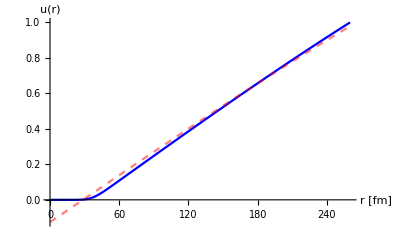

36.7141

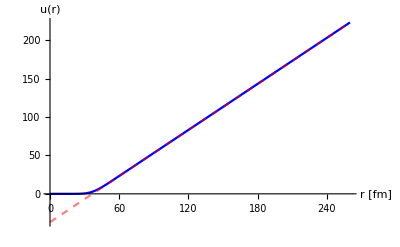

```mathematica
μ=938.92;mh2=(μ 2)/(hbar)^2;e0=0.0001;hbar=197.327053;Rmax=260;nGrid=1500;

Λ=lecs[[lecnbr]][[1]];λ=0.25 Λ^2;
α=lecs[[lecnbr]][[2]];
C0=lecs[[lecnbr]][[3]];
Print["μ = ", μ, "     hbarc = ",hbar, "     h^2/2μ = ", N[1/mh2 ],"      E_0 = ",e0,"MeV"];
Print["λ = ",λ,"fm^-2     C_0 = ",C0,"MeV    α = ",α,"fm^-2"];
(* eq.(23) OverHat[=] zero-range, zero-energy, and localized (ab)-(ab) potential *)
V0[r_]:=hbar^2/(2 μ) (4 α^2 r^2-2 α) 8 Pi^1.5 Exp[-α r^2]+C0 (2 α/(2 α+λ))^1.5 (2 Exp[-2 α r^2]-16 Pi^1.5 Exp[-3 α r^2]);
W[r_,rp_,e_]:=0;

a0=SolveSecular[e0,Rmax,nGrid,True]
ListLinePlot[{wf,wffree},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},AxesLabel->{"r [fm]","u(r)"},PlotRange->{Automatic,Automatic}]

a0=SolveSecular[0,Rmax,nGrid,True]
ListLinePlot[{wf,wffree},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},AxesLabel->{"r [fm]","u(r)"},PlotRange->{Automatic,Automatic}]
```

Λ = 1. fm^-2     C_0 = -30.9795 MeV     a_0 = 12.9802 fm

Λ = 2. fm^-2     C_0 = -117.525 MeV     a_0 = 12.9802 fm

Λ = 3. fm^-2     C_0 = -259.721 MeV     a_0 = 12.9801 fm

Λ = 4. fm^-2     C_0 = -457.556 MeV     a_0 = 12.9801 fm

Λ = 5. fm^-2     C_0 = -711.061 MeV     a_0 = 12.9801 fm

Λ = 6. fm^-2     C_0 = -1020.18 MeV     a_0 = 12.9801 fm

Λ = 7. fm^-2     C_0 = -1385.01 MeV     a_0 = 12.9801 fm

Λ = 8. fm^-2     C_0 = -1805.44 MeV     a_0 = 12.9801 fm

Λ = 9. fm^-2     C_0 = -2281.56 MeV     a_0 = 12.9801 fm

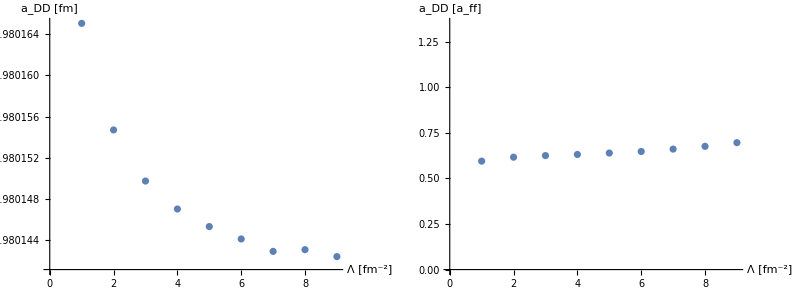

```mathematica
addofL={};μ=938.92;mh2=(μ 2)/(hbar)^2;e0=0.0;hbar=197.327053;
Do[
Λ=pot[[1]];λ=0.25 Λ^2;
C0=pot[[3]];α=pot[[2]];
V0[r_]:=hbar^2/(2 μ) (4 α^2 r^2-2 α) 8 Pi^1.5 Exp[-α r^2]+C0 (2 α/(2 α+λ))^1.5 (2 Exp[-2 α r^2]-16 Pi^1.5 Exp[-3 α r^2]);
W[r_,rp_,e_]:=0;
a0=SolveSecular[e0,Rmax,nGrid,True];
AppendTo[addofL,{Λ,a0}];
Print["Λ = ",Λ," fm^-2     C_0 = ",C0," MeV     a_0 = ",a0," fm"]
,{pot,lecs}]
addbyaffofL=Table[{lecs[[n]][[1]],addofL[[n]][[2]]/affofL[[n]][[2]]},{n,Length[lecs]}];
Grid[{{ListPlot[addofL,AxesLabel->{"Λ [fm^-2]","a_DD [fm]"}],ListPlot[addbyaffofL,PlotRange->{Automatic,{0,2.1 Mean[addbyaffofL[[All,2]]]}},AxesLabel->{"Λ [fm^-2]","a_DD [a_ff]"}]}}]
```

single-channel RGM (non-local)

μ = 938.92     hbarc = 197.327     h^2/2μ = 20.7355      E_0 = 0.001MeV

λ = 6.25fm^-2     C_0 = -711.061MeV    α = 0.0288fm^-2

6.36626

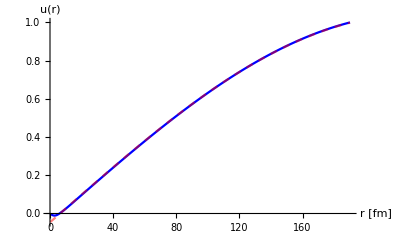

6.66452

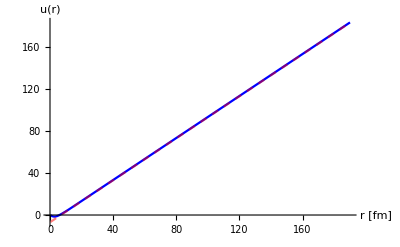

```mathematica
μ=938.92;mh2=(μ 2)/(hbar)^2;e0=0.001;hbar=197.327053;Rmax=190;nGrid=900;

Λ=lecs[[lecnbr]][[1]];λ=0.25 Λ^2;
α=8 lecs[[lecnbr]][[2]];
C0=lecs[[lecnbr]][[3]];
Print["μ = ", μ, "     hbarc = ",hbar, "     h^2/2μ = ", N[1/mh2 ],"      E_0 = ",e0,"MeV"];
Print["λ = ",λ,"fm^-2     C_0 = ",C0,"MeV    α = ",α,"fm^-2"];
(* eq.(21) *)
V0[r_]:=2 C0 (2 α/(2 α+λ))^1.5 Exp[-2 α λ/(2 α+λ) r^2];
(* eq.(22) with partial-wave-projection coefficients *)
W[r_,rp_,e_]:=(4π r rp) ( 8 α^(3/2)(hbar^2/(2 μ) (4 α^2 r^2-2 α)+e0)ⅇ^(-α(rp^2+r^2))-2 C0(2 α/(2 α+λ))^1.5 ⅇ^(-α(rp^2+(2α+3λ)/(2α+λ)r^2)));

a0=SolveSecular[e0,Rmax,nGrid,False]
ListLinePlot[{wf,wffree},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},AxesLabel->{"r [fm]","u(r)"},PlotRange->{Automatic,Automatic}]

a0=SolveSecular[0.0,Rmax,nGrid,False]
ListLinePlot[{wf,wffree},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},AxesLabel->{"r [fm]","u(r)"},PlotRange->{Automatic,Automatic}]
```

Λ = 1. fm^-2     C_0 = -30.9795 MeV     a_DD = 1.0259 fm     a_ff = 21.8387 fm

Λ = 2. fm^-2     C_0 = -117.525 MeV     a_DD = 1.89229 fm     a_ff = 21.0723 fm

Λ = 3. fm^-2     C_0 = -259.721 MeV     a_DD = 2.02064 fm     a_ff = 20.7748 fm

Λ = 4. fm^-2     C_0 = -457.556 MeV     a_DD = 2.12491 fm     a_ff = 20.5714 fm

Λ = 5. fm^-2     C_0 = -711.061 MeV     a_DD = 2.20051 fm     a_ff = 20.3192 fm

Λ = 6. fm^-2     C_0 = -1020.18 MeV     a_DD = 2.25465 fm     a_ff = 20.0526 fm

Λ = 7. fm^-2     C_0 = -1385.01 MeV     a_DD = 2.29441 fm     a_ff = 19.6587 fm

Λ = 8. fm^-2     C_0 = -1805.44 MeV     a_DD = 2.32455 fm     a_ff = 19.2162 fm

Λ = 9. fm^-2     C_0 = -2281.56 MeV     a_DD = 2.34807 fm     a_ff = 18.6582 fm

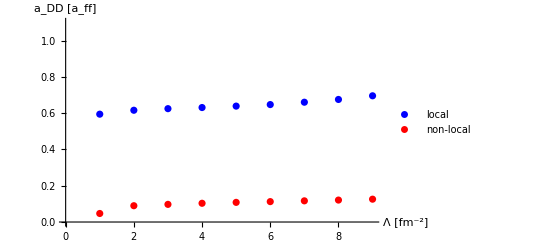

```mathematica
addofLNL={};μ=938.92;mh2=(μ 2)/(hbar)^2;e0=0.00001;hbar=197.327053;
Rmax=200;nGrid=400;iter=1;
Do[
Λ=pot[[1]];λ=0.25 Λ^2;
C0=pot[[3]];α=118 pot[[2]];
V0[r_]:=2 C0 (2 α/(2 α+λ))^1.5 Exp[-2 α λ/(2 α+λ) r^2];
(* eq.(22) with partial-wave-projection coefficients *)
W[r_,rp_,e_]:=(4π r rp) ( 8 α^(3/2)(hbar^2/(2 μ) (4 α^2 r^2-2 α)+e0)ⅇ^(-α(rp^2+r^2))-2 C0(2 α/(2 α+λ))^1.5 ⅇ^(-α(rp^2+(2α+3λ)/(2α+λ)r^2)));a0=SolveSecular[e0,Rmax,nGrid,False];
AppendTo[addofLNL,{Λ,a0}];
Print["Λ = ",Λ," fm^-2     C_0 = ",C0," MeV     a_DD = ",a0," fm     a_ff = ",affofL[[iter]][[2]]," fm"];iter=iter+1;
,{pot,lecs}]
addbyaffofLNL=Table[{lecs[[n]][[1]],addofLNL[[n]][[2]]/affofL[[n]][[2]]},{n,Length[lecs]}];
ListPlot[{addbyaffofL,addbyaffofLNL},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},PlotLegends->{"local","non-local"},PlotRange->{Automatic,{0,1.1 (*Max[addbyaffofLNL[[All,2]]]*)}},AxesLabel->{"Λ [fm^-2]","a_DD [a_ff]"}]
```